# Root Mean Squares

## By Jesse Elder, Donart Tota, Arbind Shrestha

First and foremost, we define our original recursive sequence that defines the Root Mean Square. This function which we call provingLimit takes 3 arguments: a position 1 for the sequence, a position 2 for the sequence, and a counter giving the maximum number iterations desired of the sequence.

```mathematica
provingLimit[b1_,b2_,n_]:=Module[{aN, steps=n, a1=b1,a2=b2},
(* This loop will do calculate Subscript[a, n] *)
While[steps>1,
aN=Sqrt[(a1^2+a2^2)/2];
a1=a2;
a2=aN;
steps=steps-1
];
Return[aN];
]
```

This next portion tests out the sequence given initial conditions 10 and 2 ranging out to the 1000th iteration of the Root Mean Recursive Sequence. We also do a preliminary run of the proposed limit of this sequence.

```mathematica
N[provingLimit[10,2,1000],50]
Sqrt[108/3]
```

6.

6

The proposed limit of this sequence is (n→∞)^(lim a_n)= √((a_1^2+2 a_2^2)/3)
In the following lines we create a function to represent this limit given the two initial conditions.

```mathematica
(* the deffinition of the limit as shown in the paper *)
limitItself[a1_,a2_] :=Module[{},
Sqrt[(a1^2+2*a2^2)/3]
]
limitItself[10,2]
```

6

This line attempts to show the equality of the Root Mean Sequence after a large number of iterations (100) to the limit found given the same intial conditions. Clearly this is true for initialconditions a1=10 and a2=2.

```mathematica
(* Checking if it works for one value *)
N[provingLimit[10,2,100],10]==limitItself[10,2]
```

True

testLimit accepts a list of numbers as an argument such that it takes the first 2 numbers in the list and tests the equality of the sequence with these initial conditions to the proposed limit with the same initial conditions. When randomInt is input as the argument of testLimit, it means that the equality is tested for 100 sets of random initial conditions ranging from 1 to 100000000. As can be seen by the resulting list of “True” return values, for all 100 of these sets random initial conditions, the Root Mean Sequence at high n is equal to the proposed limit.

```mathematica
randomInt= RandomInteger[{1,100000000},200];
testLimit[l1_] := Module[{},
n=1;
While[n<200,
a1=l1[[n]];
a2=l1[[n+1]];
Print[N[provingLimit[a1,a2,100],10]==limitItself[a1,a2]];
n=n+1;
]
]
```

```mathematica
testLimit[randomInt]
```

True

True

True

«47 more identical outputs»

The theorem holds for all random values.

## Graphing how a_n changes.

In this part we will see how a_n changes as we increase the number of steps and we will see how it settles. We will save all the a_n values in a list and submit it.

```mathematica
provingLimit2[b1_,b2_,n_]:=Module[{aN, steps=n, a1=b1,a2=b2},
l1={};
While[steps>1,
aN=Sqrt[(a1^2+a2^2)/2];
AppendTo[l1,aN];
a1=a2;
a2=aN;
steps=steps-1;
];
Return[l1];
]
```

This confirms graphically that there is a clear, defined limit for the Root Mean Square.

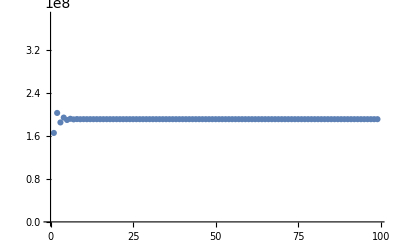

```mathematica
x=provingLimit2[2142342,234234234,100];
ListPlot[x]
```

# Expansions and Generalizations

In this next portion of our exploration and proof of the Root Mean Square Recursive Sequence, we approach the original sequence graphically, and then we proceed to expand the sequence and limit to a Root Mean Cubic Recursive Sequence.

Let (a_n)n≥1 be the sequence defined recursively by a_(n+1) = ((a_n^3+(a_(n-1))^3)/2)^(1/3) for n ≥ 2, with a_1 and a_2 two positive numbers as initial values. Then lim_(n→∞)  a_n =((a_1^3+a_2^3)/2)^(1/3)

```mathematica
provingLimit4[x1_,x2_,n_]:=Module[{aN, steps=n, a1=x1,a2=x2},
While[steps>1,
aN=CubeRoot[(a1^3+a2^3)/2];
a1=a2;
a2=aN;
steps=steps-1
];
Return[aN];
]
```

```mathematica
N[provingLimit4[10,2,100],20]
```

6.9703965233175282159

```mathematica
(*In the following lines we create a function to represent this limit given the two initial conditions.*)
limitItself4[x1_,x2_] :=Module[{},
CubeRoot[(x1^3+2*x2^3)/3]
]
```

```mathematica
N[limitItself4[10,2],20]
```

6.9703965233175282159

## This line attempts to show the equality of the Root Mean Sequence after a large number of iterations (100) to the limit found given the same initial conditions. Clearly this is true for initial conditions a1 = 10 and a2 = 2.

```mathematica
N[provingLimit4[10,2,100],10]==limitItself4[10,2]
```

True

## testLimit4 accepts a list of numbers as an argument such that it takes the first 2 numbers in the list and tests the equality of the sequence with these initial conditions to the proposed limit with the same initial conditions. When randomInt is input as the argument of testLimit, it means that the equality is tested for 50 sets of random initial conditions ranging from 1 to 100000000. As can be seen by the resulting list of "True" return values, for all 50 of these sets random initial conditions, the Root Mean Sequence at high n is equal to the proposed limit.

```mathematica
randomInt4= RandomInteger[{1,100000000},50];
testLimit4[l1_] := Module[{},
n=1;
While[n<50,
a1=l1[[n]];
a2=l1[[n+1]];
Print[N[provingLimit4[a1,a2,100],10]==limitItself4[a1,a2]];
n=n+1;
]
]
```

```mathematica
testLimit4[randomInt4]
```

True

True

True

«46 more identical outputs»

```mathematica
(*---------------------Huge expansion!---------------------*)
```

In our final section, we will prove that the (adjusted) limit holds for many different powers of a1 and a2. In order to do this, we define a function that is distinctly similar to the original sequence definition, but it takes one additional argument x. This argument x is the desired power for the sequence to follow (cubic, quartic, etc.). 
In total, the sequence follows this pattern: 	a_(n+1)=√((a_1^x+a_2^x)/2)
After consulting related literature, we found that the limit is defined similarly for sequences of this form:
					(n→∞)^(lim a_n)= ((a_1^x+2 a_2^x)/3)^(1/x)
We will prove that in future lines.

```mathematica
provingLimit3[b1_,b2_,x_, n_]:=Module[{aN, steps=n, a1=b1,a2=b2},
While[steps>1,
aN=((a1^x+a2^x)/2)^(1/x);
a1=a2;
a2=aN;
steps=steps-1
];
Return[aN];
]
```

This generates a 10th power sequence with initial conditions 10, 5 out to the 100th iteration.

```mathematica
N[provingLimit3[10,5,10,100],5]
```

8.9613

Next we define the generalized limit.

```mathematica
limitItself3[a1_,a2_,x_] :=Module[{},
((a1^x+2*a2^x)/3)^(1/x)
]
```

```mathematica
N[limitItself3[10,5, 10],5]
```

8.9613

```mathematica
(* Here we chose random starting numbers and random powers from 1 to 1000 and we see if our theorem works. *)
randomInt= RandomInteger[{1,1000},100];
testLimit[l1_] := Module[{x1},
n=1;
While[n<100,
a1=l1[[n]];
a2=l1[[n+1]];
x1=l1[[n+2]];
Print[N[provingLimit3[a1,a2,x1,50],10]==limitItself3[a1,a2,x1]];
n=n+3;
]
]
```

```mathematica
testLimit[randomInt]
```

True

True

True

«30 more identical outputs»